# Minkowski diagram

ino bebin

## Initiation

### Scale

```mathematica
n=1000;
```

```mathematica
scale=n/10;
```

### Ratio of relative velocity v to the speed of light c

```mathematica
β=0.1;
```

```mathematica
θ=ArcTan[β] 180/π
```

5.71059

### Speed of light

```mathematica
c=299792458;
```

### Square of the spacetime interval

```mathematica
SquareInterval[ev1_,ev2_]:=(ev2[[1]]-ev1[[1]])^2-(ev2[[2]]-ev1[[2]])^2-(ev2[[3]]-ev1[[3]])^2-(ev2[[4]]-ev1[[4]])^2
```

### Δx/Δt

```mathematica
Δx[ev1_,ev2_]:=ev2[[2]]-ev1[[2]]
```

```mathematica
Δt[ev1_,ev2_]:=(ev2[[1]]-ev1[[1]])/c
```

### Lorentz transformation

```mathematica
Subscript[Λ, x]=({{γ, -β γ, 0, 0}, {-β γ, γ, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}})/.γ->1/(√(1-β^2));
```

### Causal Structure

```mathematica
CausalStructure[ev1_,ev2_]:=If[SquareInterval[ev1,ev2]>0,Print["Time-like interval"],If[SquareInterval[ev1,ev2]<0,Print["Space-like interval"],Print["Light-like interval"]]]
```

## Events in S

```mathematica
e1 = {2 10^-6 c, 300,0,0}//N
```

{599.585,300.,0.,0.}

```mathematica
e2 = {3 10^-6 c, 500,0,0}//N
```

{899.377,500.,0.,0.}

```mathematica
SquareInterval[e1,e2]//N
```

49875.5

```mathematica
CausalStructure[e1,e2]
```

Time-like interval

```mathematica
Δx[e1,e2]/Δt[e1,e2]
```

2.×10^8

## Events in S’

```mathematica
e1'=Subscript[Λ, x].e1
```

{572.454,241.251,0.,0.}

```mathematica
e2'=Subscript[Λ, x].e2
```

{853.656,412.128,0.,0.}

```mathematica
SquareInterval[e1',e2']//N
```

49875.5

```mathematica
CausalStructure[e1',e2']
```

Time-like interval

```mathematica
Δx[e1',e2']/Δt[e1',e2']
```

1.82174×10^8

## Graphics

### e1e2

```mathematica
e1e2=ListPlot[{{e1[[2]],e1[[1]]},{e2[[2]],e2[[1]]}},Joined->True,MeshStyle->Red,PlotMarkers->{Automatic,Medium}];
```

```mathematica
e1text=Graphics[{Red,Text["Event 1",{0,30}+{e1[[2]],e1[[1]]}]}];
```

```mathematica
e2text=Graphics[{Red,Text["Event 2",{0,30}+{e2[[2]],e2[[1]]}]}];
```

### e1’e2’

```mathematica
e1e2'=ListPlot[{{e1'[[2]],e1'[[1]]},{e2'[[2]],e2'[[1]]}},Joined->True,MeshStyle->Red,PlotMarkers->{Automatic,Medium}];
```

```mathematica
e1text'=Graphics[{Red,Text["Event 1",{0,30}+{e1'[[2]],e1'[[1]]}]}];
```

```mathematica
e2text'=Graphics[{Red,Text["Event 2",{0,30}+{e2'[[2]],e2'[[1]]}]}];
```

### S

```mathematica
s=Graphics[{
(*xAxis*)Arrow[{{0,0},{n,0}}],
Text[Style["x",20,Italic],{n,0},{-1,0}],
(*ctAxis*)Arrow[{{0,0},{0,n}}],Text[Style["ct",20,Italic],{0,n},{0,-1}],
(*x=ct*)Red,Line[{{0,0},{n,n}}],Text[Style["x=ct",15,Italic],{n,n},{-1,-1}],
(*xGrid*)Thickness[Small],Dashed,Pink,Line[{{0,#},{n,#}}]&/@Range[0,n,scale],
(*ctGrid*)Thickness[Small],Dashed,Pink,Line[{{#,0},{#,n}}]&/@Range[0,n,scale]
}];
```

```mathematica
e1ct=Graphics[{Thickness[Small],Dashed,Blue,Line[{{e1[[2]],0},{e1[[2]],e1[[1]]}}]}];
```

```mathematica
e1x=Graphics[{Thickness[Small],Dashed,Blue,Line[{{0,e1[[1]]},{e1[[2]],e1[[1]]}}]}];
```

```mathematica
e2ct=Graphics[{Thickness[Small],Dashed,Blue,Line[{{e2[[2]],0},{e2[[2]],e2[[1]]}}]}];
```

```mathematica
e2x=Graphics[{Thickness[Small],Dashed,Blue,Line[{{0,e2[[1]]},{e2[[2]],e2[[1]]}}]}];
```

### S’

```mathematica
s'=Graphics[{
(*x'Axis*)Arrow[{{0,0},{n,n β}}],Text[Style["x'",20,Italic],{n,n β},{-1,0}],
(*ct'Axis*)Arrow[{{0,0},{n β,n}}],Text[Style["ct'",20,Italic],{n β,n},{0,-1}],
(*x=ct*)Red,Line[{{0,0},{n+n β,n+n β}}],Text[Style["x=ct",15,Italic],{n+n β,n+n β},{-1,-1}],
(*xGrid*)Thickness[Small],Dashed,Pink,Line[{{# β,#},{n+# β,#+n β}}]&/@Range[0,n,scale],
(*ctGrid*)Thickness[Small],Dashed,Pink,Line[{{#,# β},{#+n β,n+# β}}]&/@Range[0,n,scale]
}];
```

```mathematica
e1ct'=Graphics[{Thickness[Small],Dashed,Blue,Line[{{(  e1'[[2]]- β e1'[[1]])/(1-β^2),( β e1'[[2]]- β^2 e1'[[1]])/(1-β^2)},{e1'[[2]],e1'[[1]]}}]}];
```

```mathematica
e1x'=Graphics[{Thickness[Small],Dashed,Blue,Line[{{ β( β e1'[[2]]- e1'[[1]])/(β^2-1),( β e1'[[2]]- e1'[[1]])/(β^2-1)},{e1'[[2]],e1'[[1]]}}]}];
```

```mathematica
e2ct'=Graphics[{Thickness[Small],Dashed,Blue,Line[{{(  e2'[[2]]- β e2'[[1]])/(1-β^2),( β e2'[[2]]- β^2 e2'[[1]])/(1-β^2)},{e2'[[2]],e2'[[1]]}}]}];
```

```mathematica
e2x'=Graphics[{Thickness[Small],Dashed,Blue,Line[{{ β( β e2'[[2]]- e2'[[1]])/(β^2-1),( β e2'[[2]]- e2'[[1]])/(β^2-1)},{e2'[[2]],e2'[[1]]}}]}];
```

## Show S

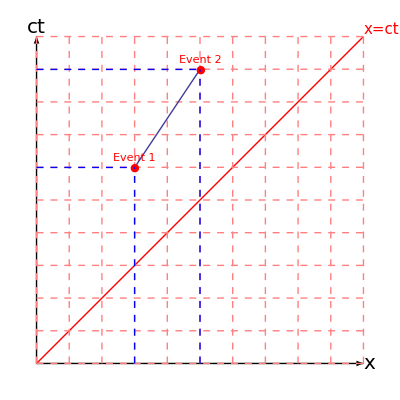

```mathematica
Show[s,e1e2,e1ct,e1x,e2ct,e2x,e1text,e2text]
```

## Show S’

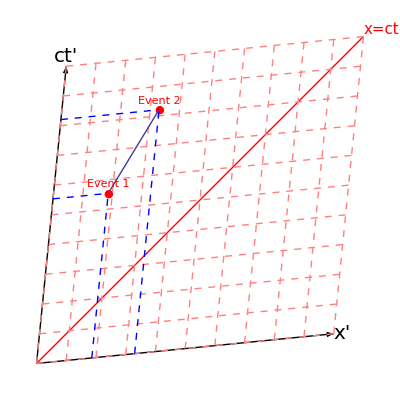

```mathematica
Show[s',e1e2',e1ct',e1x',e2ct',e2x',e1text',e2text']
```